```mathematica
dungeon=Graph[Table[i,{i,0,499}],{0<->4,0<->8,0<->3,0<->1,8<->16,3<->21,3<->11,11<->80,80<->83,83<->99,99<->122,21<->36,36<->41,41<->76,41<->69,69<->72,72<->89,89<->104,104<->126,104<->105,105<->129,105<->225,129<->190,190<->222,222<->274,225<->226,226<->260,260<->266,266<->379,126<->135,126<->158,158<->164,158<->235,164<->180,135<->149,149<->191,149<->156,191<->193,193<->203,193<->241,203<->269,269<->315,315<->406,315<->335,406<->410,335<->346,335<->378,378<->466,466<->472,472<->481,472<->495,481<->485,241<->256,256<->279,256<->327,279<->323,327<->362,362<->395,362<->469,395<->423,156<->209,156<->177,209<->213,213<->217,213<->216,217<->271,271<->310,216<->236,236<->263,236<->258,263<->299,263<->372,299<->356,299<->312,312<->347,312<->355,355<->457,457<->494,347<->375,347<->437,375<->413,375<->393,413<->419,413<->478,478<->493,356<->405,405<->432,432<->449,432<->473,449<->450,372<->433,177<->215,215<->243,215<->220,220<->230,220<->314,314<->339,339<->404,404<->482,482<->484,230<->344,344<->359,344<->367,367<->462,462<->486,359<->458,458<->463,418<->463,418<->479,349<->418,284<->349,284<->470,284<->368,254<->284,368<->436,368<->465,205<->254,162<->205,128<->162,128<->194,92<->128,194<->227,81<->92,92<->100,81<->137,81<->108,45<->81,108<->167,167<->187,187<->303,187<->301,303<->352,303<->333,333<->358,333<->365,358<->397,358<->399,399<->400,400<->492,365<->447,365<->414,137<->168,168<->207,168<->171,207<->297,45<->85,40<->45,40<->74,19<->40,19<->32,15<->19,13<->15,13<->14,9<->13,14<->17,14<->47,17<->33,17<->46,17<->28,28<->60,28<->30,60<->64,64<->111,64<->102,111<->121,111<->114,114<->120,121<->148,121<->123,148<->163,148<->178,163<->257,163<->165,163<->228,165<->169,165<->197,169<->385,169<->223,223<->483,197<->199,199<->281,199<->318,318<->340,318<->394,340<->374,394<->426,394<->422,422<->461,281<->350,281<->392,392<->408,408<->443,443<->477,350<->425,425<->434,228<->253,253<->285,257<->388,386<->388,354<->386,354<->361,321<->354,361<->366,366<->497,321<->334,304<->321,334<->384,384<->435,240<->304,233<->240,152<->233,152<->196,147<->152,196<->278,196<->224,224<->287,287<->313,287<->353,353<->380,380<->476,380<->445,445<->480,445<->446,278<->338,139<->147,147<->154,154<->192,154<->184,192<->239,239<->255,239<->336,336<->373,336<->421,138<->139,139<->176,138<->143,123<->138,102<->107,107<->141,141<->175,175<->200,200<->328,200<->204,46<->61,46<->79,79<->106,106<->161,106<->112,112<->210,112<->124,124<->174,174<->277,174<->221,277<->331,331<->387,387<->444,221<->250,221<->342,250<->295,250<->289,289<->319,289<->324,324<->391,324<->411,391<->489,391<->396,489<->491,411<->428,428<->429,428<->452,429<->451,319<->441,295<->332,332<->351,351<->417,351<->453,417<->442,342<->357,161<->166,166<->208,208<->307,61<->82,61<->63,82<->155,155<->185,185<->195,185<->292,292<->316,316<->341,63<->140,7<->9,1<->7,7<->12,1<->2,1<->22,2<->5,2<->10,5<->50,5<->6,6<->62,6<->23,23<->57,23<->58,57<->94,57<->68,94<->97,94<->113,113<->145,145<->183,97<->110,97<->153,110<->118,110<->157,118<->133,118<->218,133<->234,133<->151,234<->280,234<->247,234<->259,259<->291,291<->306,306<->415,247<->369,151<->188,144<->218,218<->252,252<->261,261<->345,345<->409,409<->488,134<->144,65<->134,62<->65,50<->66,50<->70,66<->96,96<->179,179<->181,179<->201,201<->206,206<->232,232<->265,232<->244,265<->268,265<->273,268<->276,276<->459,276<->322,322<->424,459<->467,273<->296,273<->298,298<->360,360<->364,364<->401,401<->420,401<->427,420<->464,427<->438,427<->474,438<->448,448<->475,448<->490,475<->496,296<->382,296<->308,382<->455,308<->317,308<->337,317<->416,337<->383,383<->460,244<->264,264<->290,70<->116,70<->87,87<->117,117<->127,117<->170,170<->182,182<->211,211<->248,248<->272,127<->212,127<->173,212<->229,229<->237,237<->370,173<->202,202<->267,202<->249,267<->302,302<->402,402<->403,403<->439,116<->159,10<->38,12<->20,12<->18,20<->31,20<->26,26<->27,27<->55,55<->56,56<->73,56<->67,67<->84,84<->86,86<->146,86<->95,95<->109,109<->136,136<->231,231<->282,231<->294,294<->363,294<->311,311<->389,311<->499,73<->132,132<->172,31<->37,37<->91,37<->42,42<->51,51<->93,91<->101,18<->24,18<->34,24<->29,24<->25,25<->43,43<->77,43<->49,49<->119,119<->219,119<->131,219<->242,219<->305,305<->330,330<->348,330<->454,242<->286,286<->309,286<->288,288<->326,288<->498,309<->371,309<->377,377<->456,371<->430,430<->440,131<->329,329<->407,77<->130,29<->54,34<->35,34<->39,39<->52,39<->71,71<->115,71<->150,150<->251,115<->160,160<->214,214<->246,246<->325,246<->412,35<->44,44<->48,44<->59,59<->189,189<->275,275<->283,283<->376,376<->468,48<->53,53<->75,75<->78,75<->88,88<->103,88<->125,125<->198,125<->238,198<->270,270<->300,300<->320,320<->471,238<->381,238<->293,381<->431,78<->90,90<->98,90<->142,142<->245,245<->343,98<->186,186<->262,262<->390,390<->398,398<->487}];
```

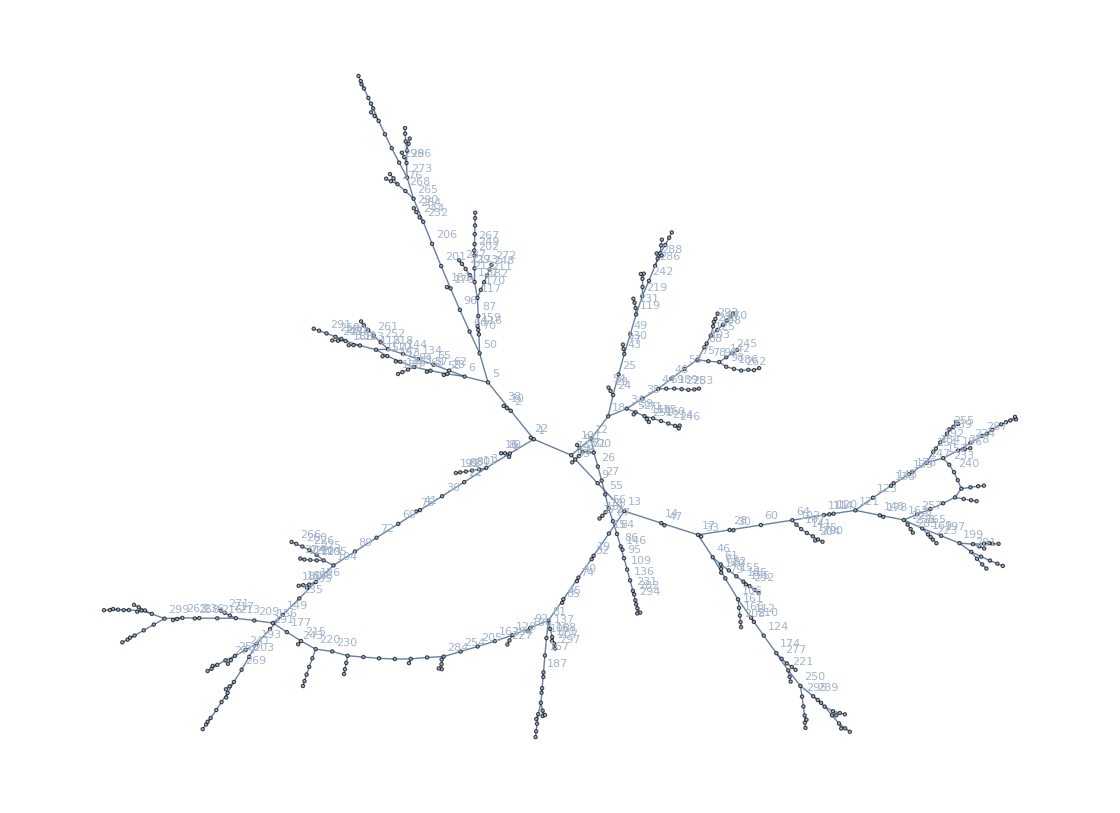

```mathematica
GraphPlot[dungeon,VertexLabels->"Name"]
```

```mathematica
shortestPath=FindShortestPath[dungeon,All,All];
```

```mathematica
distanceMatrix=GraphDistanceMatrix[dungeon];
```

```mathematica
weightedDungeon=WeightedAdjacencyGraph[distanceMatrix];
```

```mathematica
hamPath[i_,j_]:=FindHamiltonianPath[weightedDungeon,i+1,j+1]-1
```

```mathematica
fullPathFromHam[{x_,y_,z___}]:=Flatten[{shortestPath[x,y],Rest[fullPathFromHam[{y,z}]]}]
fullPathFromHam[{z___}]:={0}
fullPath[i_,j_]:=fullPathFromHam[hamPath[i,j]]
```

```mathematica
MinimalBy[Array[#&,499],Length[fullPath[0,#]]&]
```

{496}

```mathematica
fullPath[0,496]
Length@%-1
```

{0,8,16,8,0,4,0,3,11,80,83,99,122,99,83,80,11,3,21,36,41,76,41,69,72,89,104,105,129,190,222,274,222,190,129,105,225,226,260,266,379,266,260,226,225,105,104,126,158,164,180,164,158,235,158,126,135,149,191,193,241,256,279,323,279,256,327,362,469,362,395,423,395,362,327,256,241,193,203,269,315,406,410,406,315,335,346,335,378,466,472,481,485,481,472,495,472,466,378,335,315,269,203,193,191,149,156,209,213,216,236,263,299,312,347,375,413,478,493,478,413,419,413,375,393,375,347,437,347,312,355,457,494,457,355,312,299,356,405,432,449,450,449,432,473,432,405,356,299,263,372,433,372,263,236,258,236,216,213,217,271,310,271,217,213,209,156,177,215,243,215,220,314,339,404,482,484,482,404,339,314,220,230,344,367,462,486,462,367,344,359,458,463,418,479,418,349,284,368,465,368,436,368,284,470,284,254,205,162,128,194,227,194,128,92,100,92,81,137,168,171,168,207,297,207,168,137,81,108,167,187,301,187,303,333,358,399,400,492,400,399,358,397,358,333,365,447,365,414,365,333,303,352,303,187,167,108,81,45,85,45,40,74,40,19,32,19,15,13,14,17,33,17,28,30,28,60,64,111,114,120,114,111,121,148,178,148,163,165,197,199,281,392,408,443,477,443,408,392,281,350,425,434,425,350,281,199,318,394,422,461,422,394,426,394,318,340,374,340,318,199,197,165,169,223,483,223,169,385,169,165,163,228,253,285,253,228,163,257,388,386,354,361,366,497,366,361,354,321,334,384,435,384,334,321,304,240,233,152,196,278,338,278,196,224,287,313,287,353,380,476,380,445,446,445,480,445,380,353,287,224,196,152,147,154,192,239,336,373,336,421,336,239,255,239,192,154,184,154,147,139,176,139,138,143,138,123,121,111,64,102,107,141,175,200,328,200,204,200,175,141,107,102,64,60,28,17,46,79,106,161,166,208,307,208,166,161,106,112,210,112,124,174,277,331,387,444,387,331,277,174,221,342,357,342,221,250,295,332,351,417,442,417,351,453,351,332,295,250,289,319,441,319,289,324,391,396,391,489,491,489,391,324,411,428,452,428,429,451,429,428,411,324,289,250,221,174,124,112,106,79,46,61,82,155,185,292,316,341,316,292,185,195,185,155,82,61,63,140,63,61,46,17,14,47,14,13,9,7,12,20,31,37,42,51,93,51,42,37,91,101,91,37,31,20,26,27,55,56,73,132,172,132,73,56,67,84,86,146,86,95,109,136,231,282,231,294,311,499,311,389,311,294,363,294,231,136,109,95,86,84,67,56,55,27,26,20,12,18,34,35,44,48,53,75,88,125,198,270,300,320,471,320,300,270,198,125,238,293,238,381,431,381,238,125,88,103,88,75,78,90,98,186,262,390,398,487,398,390,262,186,98,90,142,245,343,245,142,90,78,75,53,48,44,59,189,275,283,376,468,376,283,275,189,59,44,35,34,39,52,39,71,150,251,150,71,115,160,214,246,412,246,325,246,214,160,115,71,39,34,18,24,29,54,29,24,25,43,77,130,77,43,49,119,131,329,407,329,131,119,219,305,330,454,330,348,330,305,219,242,286,288,326,288,498,288,286,309,377,456,377,309,371,430,440,430,371,309,286,242,219,119,49,43,25,24,18,12,7,1,22,1,2,10,38,10,2,5,6,62,65,134,144,218,252,261,345,409,488,409,345,261,252,218,118,133,234,259,291,306,415,306,291,259,234,280,234,247,369,247,234,133,151,188,151,133,118,110,157,110,97,153,97,94,113,145,183,145,113,94,57,68,57,23,58,23,6,5,50,70,116,159,116,70,87,117,170,182,211,248,272,248,211,182,170,117,127,212,229,237,370,237,229,212,127,173,202,249,202,267,302,402,403,439,403,402,302,267,202,173,127,117,87,70,50,66,96,179,181,179,201,206,232,244,264,290,264,244,232,265,268,276,459,467,459,276,322,424,322,276,268,265,273,296,308,337,383,460,383,337,308,317,416,317,308,296,382,455,382,296,273,298,360,364,401,420,464,420,401,427,474,427,438,448,490,448,475,496}

917